```mathematica
(*grades, anonymized, post-first stage processing*)
grades={{8,6,2,1,1,2,2,2,2,1,27},{6,6,0,1,2,0,2,2,1,2,22},{3,2,0,0,1,2,0,0,0,0,8},{3,4,0,0,1,2,1,2,0,0,13},{8,2,0,2,0,2,0,0,2,2,18},{4,6,4,0,2,2,2,1,1,1,23},{4,4,4,1,2,2,2,2,1,1,23},{8,4,3,1,0,2,2,2,1,1,24},{4,2,0,0,0,0,0,0,0,0,6},{8,6,4,1,2,2,2,2,2,2,31},{7,4,0,0,0,0,2,0,0,1,14},{4,5,2,1,1,0,0,0,0,0,13},{4,5,2,0,0,2,1,1,0,0,15},{6,6,1,2,1,0,2,2,2,2,24},{6,5,4,2,2,0,2,1,0,1,23},{6,6,1,0,0,0,1,0,0,0,14},{4,4,0,2,2,2,0,1,1,2,18},{5,4,0,1,1,0,0,0,0,0,11},{6,6,4,2,1,2,2,1,1,1,26},{8,4,4,2,2,0,2,2,2,2,28},{8,6,4,1,1,2,2,2,2,0,28},{8,4,4,1,2,2,1,1,1,1,25},{8,6,2,1,0,2,2,2,1,2,26},{0,0,0,0,0,0,0,1,1,1,3},{3,3,4,0,0,2,1,0,0,0,13},{4,4,4,1,0,2,0,1,1,0,17},{4,3,2,2,0,1,2,2,1,2,19},{3,3,1,2,0,2,1,0,0,0,12},{8,6,4,2,2,2,3,2,2,2,33},{3,2,0,1,1,0,2,2,1,2,14},{7,6,4,1,1,2,3,2,2,1,29}};
scores=Transpose[grades];
```

```mathematica
(*compute correlation matrix*)
corr=ConstantArray[0,{Length[scores],Length[scores]}];
For[i=1,i≤Length[scores],i++,
For[j=1,j≤Length[scores],j++,
corr[[i]][[j]]=N[Correlation[scores[[i]],scores[[j]]]];
]
]
```

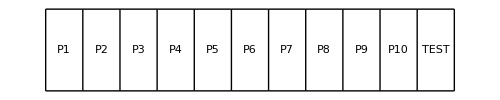
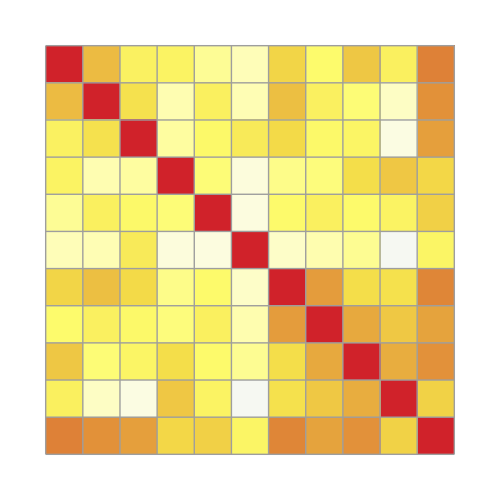
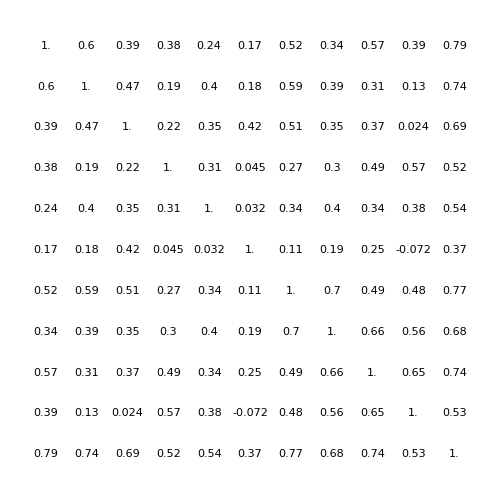
-Graphics-
-Graphics--Graphics--Graphics-

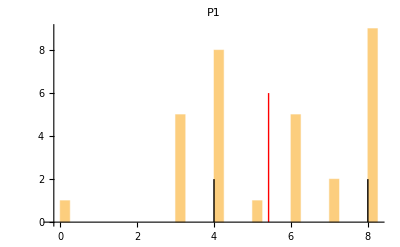
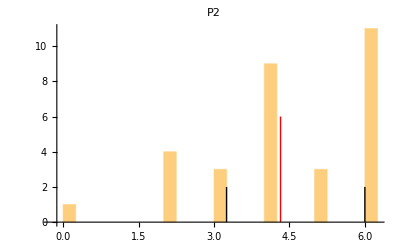
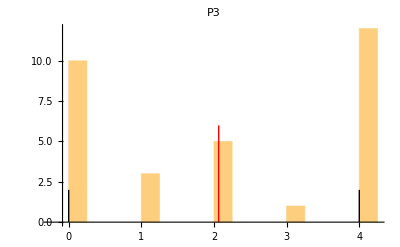
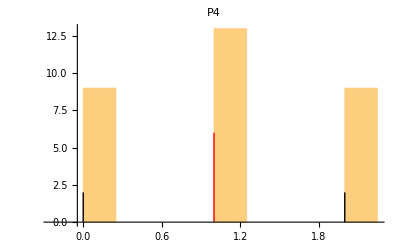
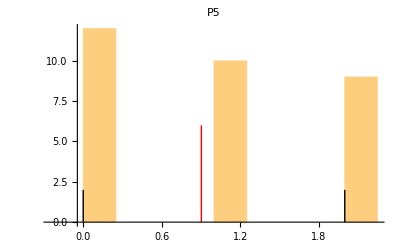
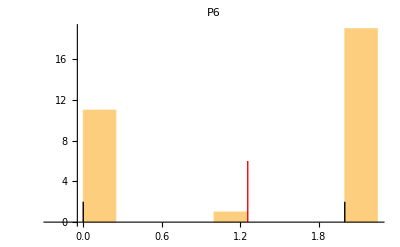
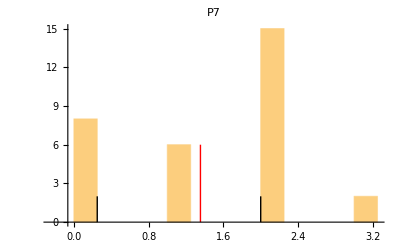
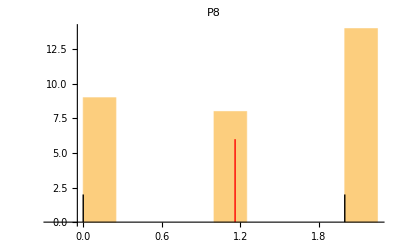

-Graphics-

```mathematica
(*labels for the correlation array*)
labels={P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,TEST};
(*Fancy picture*)
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->46,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
(*histograms,for,each,problem,&,test,as,a,whole*)
histograms={};
For[i=1,i≤Length[scores],i++,
histograms=Append[histograms,Histogram[scores[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[scores[[i]]],0},{Mean[scores[[i]]],6}}],{Directive[{Thick,Black}],Line[{{Quartiles[scores[[i]]][[1]],0},{Quartiles[scores[[i]]][[1]],2}}],Line[{{Quartiles[scores[[i]]][[3]],0},{Quartiles[scores[[i]]][[3]],2}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[Length[histograms]]]
```